```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Elastic Collisions

```mathematica
Solve[{1/2 m*vi^2==1/2 m*vf^2+1/2 M*v^2,m*vi==m*vf*Cos[θ]+M*v*Cos[ψ],0==m*vf*Sin[θ]-M*v*Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

#### First solution is physical one (based on definition of scattering angle)

```mathematica
Ef=1/2 m((2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

```mathematica
etransfer=FullSimplify[(ϵ-Ef),Assumptions->{ϵ>0,M>0,m>0}];
```

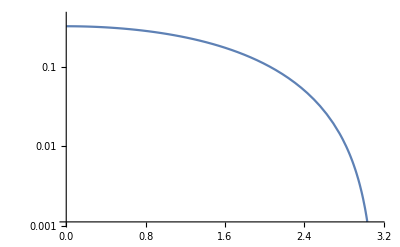

```mathematica
LogPlot[etransfer/ϵ/.{m->1,M->10},{θ,0,Pi}]
```

```mathematica
FullSimplify[ϵ/Ef/.{m->1,θ->0},Assumptions->{ϵ>0,M>0,m>0}]
```

(1+M)^2/(-1+M)^2

#### Energy transfer given by α parameter

```mathematica
(1-(M/(m+M))^2)/.{M->11180,m->1000}//N
```

0.157463

#### Below ~1 MeV neutron kinetic energy, elastic scattering may be complicated by lattice effects. So go from ~10 MeV - 1 MeV

```mathematica
Log[1/5]/Log[0.8520710059171598]
```

10.0536

#### Total distance.

```mathematica
Convert[1/(0.1 Barn*10^32/Centimeter^3)Log[x/10]/Log[n],Centimeter]/Centimeter
```

(1.×10^-7 (-Log[2]-Log[5]+Log[x]))/Log[n]

```mathematica
Convert[Sqrt[10]/(Barn*10^32/Centimeter^3),Centimeter]//N
```

3.16228×10^-8 Centimeter

```mathematica
hadronicnp=Convert[1/(0.1 Barn*10^32/Centimeter^3)Log[x/10]/Log[n],Centimeter]/Centimeter+Max[{Convert[Sqrt[10]/(Barn*10^32/Centimeter^3),Centimeter]/Centimeter,(Convert[(NIntegrate[dEdxcarbonmax^-1/.{me->0.511,n->0.8,M->11180,α->1/137,mπ->1000,Z->6},{Eπ,1,5}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter])/Centimeter}]/.n->3;
```

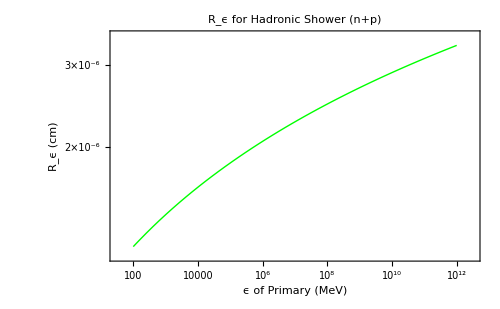

```mathematica
LogLogPlot[hadronicnp,{x,100,10^12},Frame->True,PlotStyle->{Green,Thick},PlotLabel->"R_ϵ for Hadronic Shower (n+p)",FrameLabel->{"ϵ of Primary (MeV)","R_ϵ (cm)"},FrameStyle->Black]
```